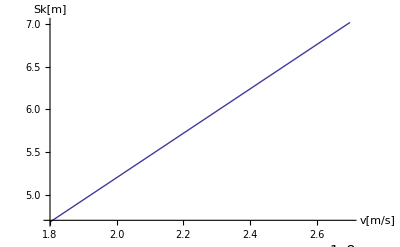

```mathematica
To = 2.6 * 10^-8;
c = 3* 10^8;
t = To / (1 - (v/c)^2)^(1/2);

Sk[v_] = v * To;
Sr[v_] = v * t;

Plot[Sk[v], {v, 0.6*c, 0.9*c},
AxesLabel->{"v[m/s]","Sk[m]"}]
```

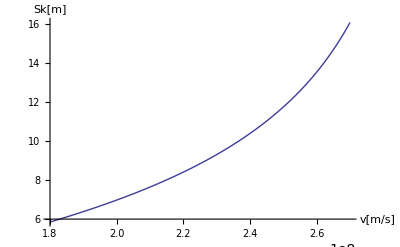

```mathematica
Plot[Sr[v], {v, 0.6*c, 0.9*c},
AxesLabel->{"v[m/s]","Sk[m]"}]
```